```mathematica
(*Now actually start*)
```

```mathematica
Ylm[l_,m_,θ_,ϕ_]:=LegendreP[l,m,Cos[θ]] Exp[I m ϕ] (-1)^m
Rlm[l_,m_,r_,θ_,ϕ_]:=(-1)^m r^l/(l+m)! Ylm[l,m,θ,ϕ];
Slm[l_,m_,r_,θ_,ϕ_]:=(-1)^m (l-m)!/r^(l+1) Ylm[l,m,θ,ϕ];
vec[r_,θ_,ϕ_]:={r Sin[θ] Cos[ϕ],r Sin[θ] Sin[ϕ],r Cos[θ]}
spher[x_,y_,z_]:={Sqrt[x^2+y^2+z^2],ArcCos[z/Sqrt[x^2+y^2+z^2]],ArcTan[x,y]}
myWignerD[{j_,m1_,m2_},α_,β_,ɣ_]:=WignerD[{j,-m1,-m2},α,β,ɣ];
(*Klm={0,kr22+I ki22, kr21+I ki21, k20,-kr21+I ki21, kr22-I ki22,0};*)
Klm={{},{0,K22,0,K20,0,K22,0}, {0,-Conjugate[K33],Conjugate[K32],-Conjugate[K31],K30,K31,K32,K33,0}};
G=(3.98199*10^14)/M;
```

```mathematica
complextorque[maxl_]:=(*(G M)/2*)Sum[Sum[Sum[Conjugate[Slm[lp,mp,r,θ,ϕ]](-1)^lp Sqrt[((lp-mpp)!(lp+mpp)!)/((lp-mp)!(lp+mp)!)]Conjugate[myWignerD[{lp,mp,mpp},a,b,c]]({I,-1,0} (lp-mpp+1)Klm[[lp]][[mpp-1+2+lp]]+{I,1,0}(lp+mpp+1)Klm[[lp]][[mpp+1+2+lp]]+2 {0,0,I}mpp Klm[[lp]][[mpp+2+lp]]),{mpp,-lp,lp}],{mp,-lp,lp}], {lp, 2,maxl}];
complextorque2=complextorque[2];complextorque3=complextorque[3];
```

(0
0
24 K22 Sin[2 c])

(-12 (K20+2 K22) Cos[c] Sin[b]
12 (K20-2 K22) Sin[b] Sin[c]
48 K22 Cos[b] Cos[2 c])

(12 (K20+2 K22) Sin[2 b] Sin[c]
12 (K20-2 K22) Cos[c] Sin[2 b]
-24 K22 (3+Cos[2 b]) Sin[2 c])

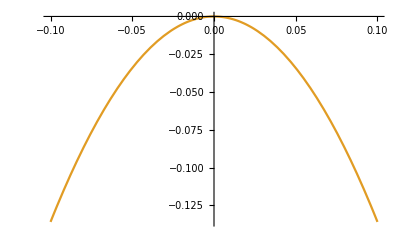

```mathematica
offsetTorque=Simplify[ExpToTrig[complextorque2/.{a->ϕ+Pi/2+x, θ->Pi/2,r->1}], Assumptions->{b>0, c>0, ϕ>0,r>0, x>0}];
Simplify[offsetTorque/.x->0]//MatrixForm
Simplify[D[offsetTorque, x]/.{x->0}]//MatrixForm
Simplify[D[offsetTorque, {x,2}]/.{x->0}]//MatrixForm
Plot[{offsetTorque[[1]]/.{b->1,ϕ->2, K22->1, c-> 0}, offsetTorque[[2]]/.{b->1,ϕ->2, K22->1, c->0, K20->-0.5}},{x,-0.1,0.1}]
```

```mathematica
(*Torque is zero for a=ϕ and β=Pi/2. Also for a=phi+pi/2 and β is anything, but only for certain c. How can torque stray from the first point?*)
```

```mathematica
Simplify[ExpToTrig[complextorque2/.{r->1, θ->Pi/2, b->0}], Assumptions->{a>0,c>0, ϕ>0}]//MatrixForm
Simplify[ExpToTrig[complextorque2/.{r->1, θ->Pi/2, a->ϕ, b->Pi/2}], Assumptions->{a>0,c>0, ϕ>0}]//MatrixForm
Simplify[ExpToTrig[complextorque2/.{r->1, θ->Pi/2, a->ϕ+3 Pi/2, c->Pi/2}], Assumptions->{a>0,b>0, ϕ>0}]//MatrixForm
```

(0
0
-24 K22 Sin[2 (a+c-ϕ)])

(0
0
0)

(0
0
0)

```mathematica
Simplify[ExpToTrig[(complextorque2+(complextorque2/.{ϕ->-ϕ}))/.{r->1, θ->Pi/2,a->Pi/2, b->Pi/2}], Assumptions->{a>0,b>0, ϕ>0,c>0}]//MatrixForm
Simplify[D[Simplify[ExpToTrig[complextorque2/.{r->1, θ->Pi/2,a->Pi/2, b->Pi/2}], Assumptions->{b>0, ϕ>0,c>0}],{ϕ}]]/.ϕ->0//MatrixForm
```

(0
0
96 K22 Cos[c] Cos[ϕ]^2 Sin[c])

(12 (K20+2 K22) Cos[c]
-12 (K20-2 K22) Sin[c]
0)

```mathematica
(*What does the torque profile look like?*)
Simplify[ExpToTrig[complextorque2/.{r->1, θ->Pi/2,a->Pi/2, b->Pi/2}], Assumptions->{b>0, ϕ>0,c>0}]//MatrixForm
```

```mathematica
secondtorque=Simplify[ExpToTrig[complextorque/.{ θ->Pi/2,r->1}], Assumptions->{a>0,b>0, c>0, ϕ>0,r>0, x>0}];
secondtorque//MatrixForm
```

(3/4 (20 ⅈ K32 Cos[b/2]^6 Cos[3 (a+c-ϕ)]-20 ⅈ Conjugate[K32] Cos[b/2]^6 Cos[3 (a+c-ϕ)]-60 ⅈ K32 Cos[b/2]^4 Cos[a+3 c-ϕ] Sin[b/2]^2+60 ⅈ Conjugate[K32] Cos[b/2]^4 Cos[a+3 c-ϕ] Sin[b/2]^2+60 ⅈ K32 Cos[b/2]^2 Cos[a-3 c-ϕ] Sin[b/2]^4-60 ⅈ Conjugate[K32] Cos[b/2]^2 Cos[a-3 c-ϕ] Sin[b/2]^4-20 ⅈ K32 Cos[3 a-3 c-3 ϕ] Sin[b/2]^6+20 ⅈ Conjugate[K32] Cos[3 a-3 c-3 ϕ] Sin[b/2]^6+4 (K20+2 K22) Cos[b] Sin[b] (-ⅈ Cos[c]+Sin[c])+4 (K20+2 K22) Cos[b] Sin[b] (ⅈ Cos[c]+Sin[c])-10 ⅈ (K31-Conjugate[K31]) Sin[b]^3 (Cos[3 a-3 ϕ]-ⅈ Sin[3 a-3 ϕ])+10 (K31-Conjugate[K31]) Sin[b]^3 (-ⅈ Cos[3 a-3 ϕ]+Sin[3 a-3 ϕ])-20 K32 Sin[b/2]^6 Sin[3 a-3 c-3 ϕ]-20 Conjugate[K32] Sin[b/2]^6 Sin[3 a-3 c-3 ϕ]-40 ⅈ (K31+3 K33) Cos[b/2] Sin[b/2]^5 (Cos[3 a-2 c-3 ϕ]-ⅈ Sin[3 a-2 c-3 ϕ])+40 ⅈ (Conjugate[K31]+3 Conjugate[K33]) Cos[b/2] Sin[b/2]^5 (Cos[3 a-2 c-3 ϕ]+ⅈ Sin[3 a-2 c-3 ϕ])+(3 K30+5 K32) Cos[b/2]^2 Sin[b/2]^4 (-20 ⅈ Cos[3 a-c-3 ϕ]-20 Sin[3 a-c-3 ϕ])+20 ⅈ (3 K30+5 Conjugate[K32]) Cos[b/2]^2 Sin[b/2]^4 (Cos[3 a-c-3 ϕ]+ⅈ Sin[3 a-c-3 ϕ])+(3 K30+5 Conjugate[K32]) Cos[b/2]^4 Sin[b/2]^2 (-20 ⅈ Cos[3 a+c-3 ϕ]-20 Sin[3 a+c-3 ϕ])+20 ⅈ (3 K30+5 K32) Cos[b/2]^4 Sin[b/2]^2 (Cos[3 a+c-3 ϕ]+ⅈ Sin[3 a+c-3 ϕ])+40 (K31+3 K33) Cos[b/2]^5 Sin[b/2] (-ⅈ Cos[3 a+2 c-3 ϕ]+Sin[3 a+2 c-3 ϕ])+40 (Conjugate[K31]+3 Conjugate[K33]) Cos[b/2]^5 Sin[b/2] (ⅈ Cos[3 a+2 c-3 ϕ]+Sin[3 a+2 c-3 ϕ])+8 (K20+2 K22) Cos[b/2] Sin[b/2]^3 (-ⅈ Cos[2 a-c-2 ϕ]+Sin[2 a-c-2 ϕ])+8 (K20+2 K22) Cos[b/2] Sin[b/2]^3 (ⅈ Cos[2 a-c-2 ϕ]+Sin[2 a-c-2 ϕ])+8 (K20+2 K22) Cos[b/2]^3 Sin[b/2] (-ⅈ Cos[2 a+c-2 ϕ]+Sin[2 a+c-2 ϕ])+8 (K20+2 K22) Cos[b/2]^3 Sin[b/2] (ⅈ Cos[2 a+c-2 ϕ]+Sin[2 a+c-2 ϕ])+6 ⅈ (K31-Conjugate[K31]) (-1+5 Cos[b]^2) Sin[b] (Cos[a-ϕ]+ⅈ Sin[a-ϕ])+6 (K31-Conjugate[K31]) (-1+5 Cos[b]^2) Sin[b] (ⅈ Cos[a-ϕ]+Sin[a-ϕ])+15 K32 Sin[b/2]^2 Sin[b]^2 Sin[a-3 c-ϕ]+15 Conjugate[K32] Sin[b/2]^2 Sin[b]^2 Sin[a-3 c-ϕ]+20 (Conjugate[K31]+3 Conjugate[K33]) Cos[b/2] (1+3 Cos[b]) Sin[b/2]^3 (-ⅈ Cos[a-2 c-ϕ]+Sin[a-2 c-ϕ])+20 (K31+3 K33) Cos[b/2] (1+3 Cos[b]) Sin[b/2]^3 (ⅈ Cos[a-2 c-ϕ]+Sin[a-2 c-ϕ])+(3 K30+5 Conjugate[K32]) (-1+10 Cos[b]+15 Cos[b]^2) Sin[b/2]^2 (-ⅈ Cos[a-c-ϕ]+Sin[a-c-ϕ])+(3 K30+5 K32) (-1+10 Cos[b]+15 Cos[b]^2) Sin[b/2]^2 (ⅈ Cos[a-c-ϕ]+Sin[a-c-ϕ])+(3 K30+5 K32) Cos[b/2]^2 (-1-10 Cos[b]+15 Cos[b]^2) (-ⅈ Cos[a+c-ϕ]+Sin[a+c-ϕ])+(3 K30+5 Conjugate[K32]) Cos[b/2]^2 (-1-10 Cos[b]+15 Cos[b]^2) (ⅈ Cos[a+c-ϕ]+Sin[a+c-ϕ])-20 K32 Cos[b/2]^6 Sin[3 (a+c-ϕ)]-20 Conjugate[K32] Cos[b/2]^6 Sin[3 (a+c-ϕ)]+20 (K31+3 K33) Cos[b/2]^3 (-1+3 Cos[b]) Sin[b/2] (-ⅈ Cos[a+2 c-ϕ]+Sin[a+2 c-ϕ])+20 (Conjugate[K31]+3 Conjugate[K33]) Cos[b/2]^3 (-1+3 Cos[b]) Sin[b/2] (ⅈ Cos[a+2 c-ϕ]+Sin[a+2 c-ϕ])+15/4 K32 Csc[b/2]^2 Sin[b]^4 Sin[a+3 c-ϕ]+15/4 Conjugate[K32] Csc[b/2]^2 Sin[b]^4 Sin[a+3 c-ϕ])
3/4 (-20 K32 Cos[b/2]^6 Cos[3 (a+c-ϕ)]-20 Conjugate[K32] Cos[b/2]^6 Cos[3 (a+c-ϕ)]+60 K32 Cos[b/2]^4 Cos[a+3 c-ϕ] Sin[b/2]^2+60 Conjugate[K32] Cos[b/2]^4 Cos[a+3 c-ϕ] Sin[b/2]^2-60 K32 Cos[b/2]^2 Cos[a-3 c-ϕ] Sin[b/2]^4-60 Conjugate[K32] Cos[b/2]^2 Cos[a-3 c-ϕ] Sin[b/2]^4+20 K32 Cos[3 a-3 c-3 ϕ] Sin[b/2]^6+20 Conjugate[K32] Cos[3 a-3 c-3 ϕ] Sin[b/2]^6+4 (K20-2 K22) Cos[b] Sin[b] (Cos[c]-ⅈ Sin[c])+4 (K20-2 K22) Cos[b] Sin[b] (Cos[c]+ⅈ Sin[c])-10 (K31+Conjugate[K31]) Sin[b]^3 (Cos[3 a-3 ϕ]-ⅈ Sin[3 a-3 ϕ])-10 (K31+Conjugate[K31]) Sin[b]^3 (Cos[3 a-3 ϕ]+ⅈ Sin[3 a-3 ϕ])-20 ⅈ K32 Sin[b/2]^6 Sin[3 a-3 c-3 ϕ]+20 ⅈ Conjugate[K32] Sin[b/2]^6 Sin[3 a-3 c-3 ϕ]+40 (K31-3 K33) Cos[b/2] Sin[b/2]^5 (Cos[3 a-2 c-3 ϕ]-ⅈ Sin[3 a-2 c-3 ϕ])+40 (Conjugate[K31]-3 Conjugate[K33]) Cos[b/2] Sin[b/2]^5 (Cos[3 a-2 c-3 ϕ]+ⅈ Sin[3 a-2 c-3 ϕ])+20 (3 K30-5 K32) Cos[b/2]^2 Sin[b/2]^4 (Cos[3 a-c-3 ϕ]-ⅈ Sin[3 a-c-3 ϕ])+20 (3 K30-5 Conjugate[K32]) Cos[b/2]^2 Sin[b/2]^4 (Cos[3 a-c-3 ϕ]+ⅈ Sin[3 a-c-3 ϕ])-20 (3 K30-5 Conjugate[K32]) Cos[b/2]^4 Sin[b/2]^2 (Cos[3 a+c-3 ϕ]-ⅈ Sin[3 a+c-3 ϕ])+20 (-3 K30+5 K32) Cos[b/2]^4 Sin[b/2]^2 (Cos[3 a+c-3 ϕ]+ⅈ Sin[3 a+c-3 ϕ])+40 (Conjugate[K31]-3 Conjugate[K33]) Cos[b/2]^5 Sin[b/2] (Cos[3 a+2 c-3 ϕ]-ⅈ Sin[3 a+2 c-3 ϕ])+40 (K31-3 K33) Cos[b/2]^5 Sin[b/2] (Cos[3 a+2 c-3 ϕ]+ⅈ Sin[3 a+2 c-3 ϕ])-8 (K20-2 K22) Cos[b/2] Sin[b/2]^3 (Cos[2 a-c-2 ϕ]+ⅈ Sin[2 a-c-2 ϕ])+(K20-2 K22) Cos[b/2] Sin[b/2]^3 (-8 Cos[2 a-c-2 ϕ]+8 ⅈ Sin[2 a-c-2 ϕ])+8 (K20-2 K22) Cos[b/2]^3 Sin[b/2] (Cos[2 a+c-2 ϕ]-ⅈ Sin[2 a+c-2 ϕ])+8 (K20-2 K22) Cos[b/2]^3 Sin[b/2] (Cos[2 a+c-2 ϕ]+ⅈ Sin[2 a+c-2 ϕ])+3 (K31+Conjugate[K31]) (3+5 Cos[2 b]) Sin[b] (Cos[a-ϕ]-ⅈ Sin[a-ϕ])+3 (K31+Conjugate[K31]) (3+5 Cos[2 b]) Sin[b] (Cos[a-ϕ]+ⅈ Sin[a-ϕ])+15 ⅈ K32 Sin[b/2]^2 Sin[b]^2 Sin[a-3 c-ϕ]-15 ⅈ Conjugate[K32] Sin[b/2]^2 Sin[b]^2 Sin[a-3 c-ϕ]-20 (K31-3 K33) Cos[b/2] (1+3 Cos[b]) Sin[b/2]^3 (Cos[a-2 c-ϕ]-ⅈ Sin[a-2 c-ϕ])-20 (Conjugate[K31]-3 Conjugate[K33]) Cos[b/2] (1+3 Cos[b]) Sin[b/2]^3 (Cos[a-2 c-ϕ]+ⅈ Sin[a-2 c-ϕ])-(3 K30-5 K32) (-1+10 Cos[b]+15 Cos[b]^2) Sin[b/2]^2 (Cos[a-c-ϕ]-ⅈ Sin[a-c-ϕ])-(3 K30-5 Conjugate[K32]) (-1+10 Cos[b]+15 Cos[b]^2) Sin[b/2]^2 (Cos[a-c-ϕ]+ⅈ Sin[a-c-ϕ])+(3 K30-5 Conjugate[K32]) Cos[b/2]^2 (-1-10 Cos[b]+15 Cos[b]^2) (Cos[a+c-ϕ]-ⅈ Sin[a+c-ϕ])+(3 K30-5 K32) Cos[b/2]^2 (-1-10 Cos[b]+15 Cos[b]^2) (Cos[a+c-ϕ]+ⅈ Sin[a+c-ϕ])-20 ⅈ K32 Cos[b/2]^6 Sin[3 (a+c-ϕ)]+20 ⅈ Conjugate[K32] Cos[b/2]^6 Sin[3 (a+c-ϕ)]+20 (Conjugate[K31]-3 Conjugate[K33]) Cos[b/2]^3 (-1+3 Cos[b]) Sin[b/2] (Cos[a+2 c-ϕ]-ⅈ Sin[a+2 c-ϕ])+20 (K31-3 K33) Cos[b/2]^3 (-1+3 Cos[b]) Sin[b/2] (Cos[a+2 c-ϕ]+ⅈ Sin[a+2 c-ϕ])+15/4 ⅈ K32 Csc[b/2]^2 Sin[b]^4 Sin[a+3 c-ϕ]-15/4 ⅈ Conjugate[K32] Csc[b/2]^2 Sin[b]^4 Sin[a+3 c-ϕ])
1/16 (3 Conjugate[K31] (ⅈ Cos[c]+Sin[c]) (5 Cos[3 a-3 b-3 ϕ]-5 Cos[3 a-b-3 ϕ]-5 Cos[3 a+b-3 ϕ]+15 Cos[a-3 b-ϕ]+Cos[a-b-ϕ]+Cos[a+b-ϕ]+5 Cos[3 (a+b-ϕ)]+15 Cos[a+3 b-ϕ]+20 ⅈ Sin[3 a-3 ϕ]-10 ⅈ Sin[3 a-2 b-3 ϕ]-10 ⅈ Sin[3 a+2 b-3 ϕ]-12 ⅈ Sin[a-ϕ]-10 ⅈ Sin[a-2 b-ϕ]-10 ⅈ Sin[a+2 b-ϕ])+6 (4 ⅈ K31 Cos[b/2]^2 Cos[a+c-ϕ]+40 ⅈ K31 Cos[b/2]^2 Cos[b] Cos[a+c-ϕ]-60 ⅈ K31 Cos[b/2]^2 Cos[b]^2 Cos[a+c-ϕ]+240 ⅈ K33 Cos[b/2]^6 Cos[3 (a+c-ϕ)]-160 ⅈ K32 Cos[b/2]^5 Cos[3 a+2 c-3 ϕ] Sin[b/2]+80 ⅈ K32 Cos[b/2]^3 Cos[a+2 c-ϕ] Sin[b/2]-240 ⅈ K32 Cos[b/2]^3 Cos[b] Cos[a+2 c-ϕ] Sin[b/2]+80 ⅈ K31 Cos[b/2]^4 Cos[3 a+c-3 ϕ] Sin[b/2]^2-4 ⅈ K31 Cos[a-c-ϕ] Sin[b/2]^2+40 ⅈ K31 Cos[b] Cos[a-c-ϕ] Sin[b/2]^2+60 ⅈ K31 Cos[b]^2 Cos[a-c-ϕ] Sin[b/2]^2-720 ⅈ K33 Cos[b/2]^4 Cos[a+3 c-ϕ] Sin[b/2]^2+80 ⅈ K32 Cos[b/2] Cos[a-2 c-ϕ] Sin[b/2]^3+240 ⅈ K32 Cos[b/2] Cos[b] Cos[a-2 c-ϕ] Sin[b/2]^3-80 ⅈ K31 Cos[b/2]^2 Cos[3 a-c-3 ϕ] Sin[b/2]^4+720 ⅈ K33 Cos[b/2]^2 Cos[a-3 c-ϕ] Sin[b/2]^4-160 ⅈ K32 Cos[b/2] Cos[3 a-2 c-3 ϕ] Sin[b/2]^5-240 ⅈ K33 Cos[3 a-3 c-3 ϕ] Sin[b/2]^6+32 K22 Sin[b]^2 Sin[2 c]-240 K33 Sin[b/2]^6 Sin[3 a-3 c-3 ϕ]-80 K32 Sin[b/2]^4 Sin[b] Sin[3 a-2 c-3 ϕ]-20 K31 Sin[b/2]^2 Sin[b]^2 Sin[3 a-c-3 ϕ]-5 K31 Csc[b/2]^2 Sin[b]^4 Sin[3 a+c-3 ϕ]+5 K32 Csc[b/2]^4 Sin[b]^5 Sin[3 a+2 c-3 ϕ]+64 K22 Sin[b/2]^4 Sin[2 a-2 c-2 ϕ]+40 Conjugate[K32] Cos[a-ϕ] Sin[b] (ⅈ Cos[2 c]+Sin[2 c]) (Cos[a-b-ϕ]+Cos[a+b-ϕ]-2 ⅈ Sin[a-ϕ])^2-30 ⅈ Conjugate[K33] (Cos[3 c]-ⅈ Sin[3 c]) (Cos[a-b-ϕ]+Cos[a+b-ϕ]-2 ⅈ Sin[a-ϕ])^3+180 K33 Sin[b/2]^2 Sin[b]^2 Sin[a-3 c-ϕ]+40 K32 Sin[b/2]^2 Sin[b] Sin[a-2 c-ϕ]+60 K32 Sin[b/2]^2 Sin[2 b] Sin[a-2 c-ϕ]-4 K31 Sin[b/2]^2 Sin[a-c-ϕ]+40 K31 Cos[b] Sin[b/2]^2 Sin[a-c-ϕ]+60 K31 Cos[b]^2 Sin[b/2]^2 Sin[a-c-ϕ]-4 K31 Cos[b/2]^2 Sin[a+c-ϕ]-40 K31 Cos[b/2]^2 Cos[b] Sin[a+c-ϕ]+60 K31 Cos[b/2]^2 Cos[b]^2 Sin[a+c-ϕ]-64 K22 Cos[b/2]^4 Sin[2 (a+c-ϕ)]-240 K33 Cos[b/2]^6 Sin[3 (a+c-ϕ)]-10 K32 Csc[b/2]^2 Sin[b]^3 Sin[a+2 c-ϕ]+60 K32 Cos[b/2]^2 Sin[2 b] Sin[a+2 c-ϕ]+45 K33 Csc[b/2]^2 Sin[b]^4 Sin[a+3 c-ϕ])))

```mathematica
firsttorque=Simplify[secondtorque/.{K33->0,K32->0,K31->0,K30->0}];
firsttorque//MatrixForm
```

(12 (K20+2 K22) Cos[a-ϕ] Sin[b] (Cos[b] Cos[a-ϕ] Sin[c]+Cos[c] Sin[a-ϕ])
12 (K20-2 K22) Cos[a-ϕ] Sin[b] (Sin[a] (-Cos[ϕ] Sin[c]+Cos[b] Cos[c] Sin[ϕ])+Cos[a] (Cos[b] Cos[c] Cos[ϕ]+Sin[c] Sin[ϕ]))
12 K22 (Sin[b]^2 Sin[2 c]+2 Sin[b/2]^4 Sin[2 (a-c-ϕ)]-2 Cos[b/2]^4 Sin[2 (a+c-ϕ)]))

```mathematica
Integrate[k33term,{c,0,2Pi}]
```

{0,0,0}

(-6 (K20+2 K22) Cos[db] (Sin[c-2 da]-Cot[1/4 (2 db+π)]^2 Sin[c+2 da]+Csc[1/4 (2 db+π)]^2 Sin[c] Sin[db]) Sin[1/4 (2 db+π)]^2
-6 (K20-2 K22) Cos[db] (Sin[c] Sin[2 da]+2 Cos[c] Cos[da]^2 Sin[db])
-24 K22 (-Cos[c] Cos[db]^2 Sin[c]+Cos[1/4 (2 db+π)]^4 Sin[2 (c+da)]+Sin[2 c-2 da] Sin[1/4 (2 db+π)]^4))

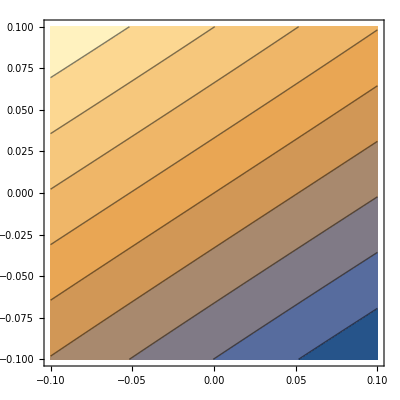

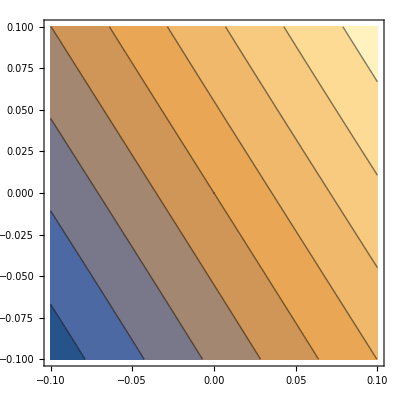

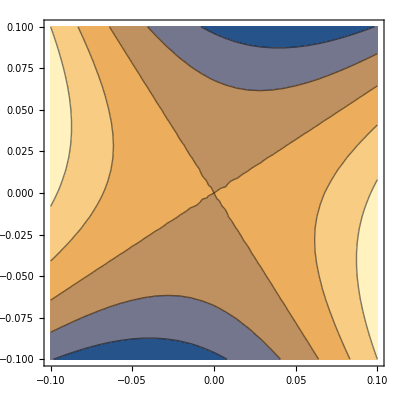

```mathematica
dTorque=Simplify[ExpToTrig[complextorque/.{a->ϕ+da,b->Pi/2+db,c->c,θ->Pi/2,ϕ->ϕ, r->1}], Assumptions->{c>0,db∈Reals,da∈Reals}];
dTorque//MatrixForm
ContourPlot[dTorque[[1]]/.{c->1,ϕ->2, K20->-0.1,K22->0.02},{da,-0.1,0.1},{db,-0.1,0.1}]
ContourPlot[dTorque[[2]]/.{c->1,ϕ->2, K20->-0.1,K22->0.02},{da,-0.1,0.1},{db,-0.1,0.1}]
ContourPlot[dTorque[[3]]/.{c->1,ϕ->2, K20->-0.1,K22->0.02},{da,-0.1,0.1},{db,-0.1,0.1}]
```

(6 K20 Sin[b] (Sin[b/2]^2 Sin[2 a-c]+Cos[b] Sin[c]+Cos[b/2]^2 Sin[2 a+c])
12 K20 Cos[a] Sin[b] (Cos[a] Cos[b] Cos[c]-Sin[a] Sin[c])
0)

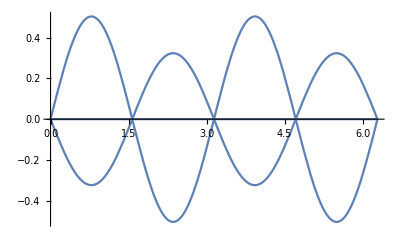

```mathematica
Simplify[ExpToTrig[complextorque/.{θ->Pi/2,K22->0,r->1,ϕ->0}], Assumptions->{b>0, c>0, ϕ>0,r>0,a>0}]//MatrixForm
Plot[complextorque/.{θ->Pi/2,K20->-0.1,K22->0,c->1,b->Pi/2,ϕ->0,r->1},{a,0,2Pi}]
```

(12 (K20+2 K22) Cos[c] | -12 (K20-2 K22) Sin[c] | 0
-12 (K20+2 K22) Sin[c] | -12 (K20-2 K22) Cos[c] | 0)

{-12 (-2 K22 Cos[c]+√(K20^2-2 K22^2+2 K22^2 Cos[2 c])),12 (2 K22 Cos[c]+√(K20^2-2 K22^2+2 K22^2 Cos[2 c]))}

(((-K20 Cos[c]+√(K20^2-2 K22^2+2 K22^2 Cos[2 c])) Csc[c])/(K20+2 K22) | 1
-((K20 Cos[c]+√(K20^2-2 K22^2+2 K22^2 Cos[2 c])) Csc[c])/(K20+2 K22) | 1)

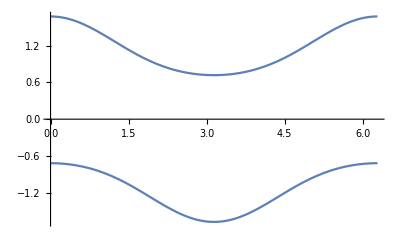

```mathematica
grad=Simplify[ExpToTrig[{D[dTorque,da],D[dTorque,db]}/.{da->0,db->0}],Assumptions->{da>0,db>0,c>0,ϕ>0}];
grad//MatrixForm
cutMatrix=grad[[All,;;2]];
evals=Simplify[Eigenvalues[cutMatrix]]
evecs=Simplify[Eigenvectors[cutMatrix]]//MatrixForm
Plot[evals/.{K22->0.02,K20->-0.1},{c,0,2Pi}]
```

```mathematica
(*What if what I should really look for is when dot of torque to velocity is zero?*)
dottedTorque=Simplify[ExpToTrig[Dot[complextorque/.{ϕ->0,θ->Pi/2,r->1}, {Cos[a]Sin[b],Sin[a]Sin[b],Cos[b]}]],Assumptions->{a>0,b>0,c>0}];
dottedTorque
```

6 (Sin[b/2]^2 Sin[b]^2 (K20 Sin[a-c]+2 K22 Sin[3 a-c])+2 Cos[b/2]^4 (2 K22 Sin[a+c]+K20 Sin[3 a+c])+Cos[b] ((K20-2 K22) Cos[c] Sin[a] Sin[b]^2+4 K22 Sin[b/2]^4 Sin[2 a-2 c]+K20 Cos[a] Sin[b]^2 Sin[c]+2 K22 Cos[a] Sin[b]^2 Sin[c]+2 K22 Sin[b]^2 Sin[2 c]-4 K22 Cos[b/2]^4 Sin[a+c]-4 K22 Cos[b/2]^4 Sin[2 (a+c)]-2 K20 Cos[b/2]^4 Sin[3 a+c]))

```mathematica
Simplify[dottedTorque/.{b->Pi/2}]
cint=Simplify[Integrate[Simplify[dottedTorque^2],{c,0,2Pi}]];
```

6 (2 K22 Cos[a-c]+K20 Cos[a+c]) Sin[2 a]

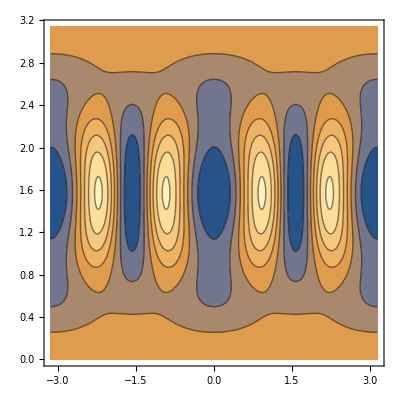

```mathematica
ContourPlot[cint/.{K22->0.02,K20->-0.1},{a,-Pi,Pi},{b,0,Pi}]
```

```mathematica
(*Blue of the above is when torque is orthogonal to spin for all c. When torque zero for all c?*)
mag =Integrate[Simplify[ExpToTrig[Dot[complextorque,complextorque]/.{ϕ->0,θ->Pi/2,r->1}],Assumptions{a>0,b>0,c>0}],{c,0,2Pi},Assumptions->{c>0}]
```

36 π (-3+Cos[2 Conjugate[a]]-2 Cos[Conjugate[a]]^2 Cos[2 Conjugate[b]]) (K22^2 (-3+Cos[2 Conjugate[a]])+2 Cos[Conjugate[a]]^2 (K22^2 (-2+Cos[2 Conjugate[b]])-K20^2 Sin[Conjugate[b]]^2))

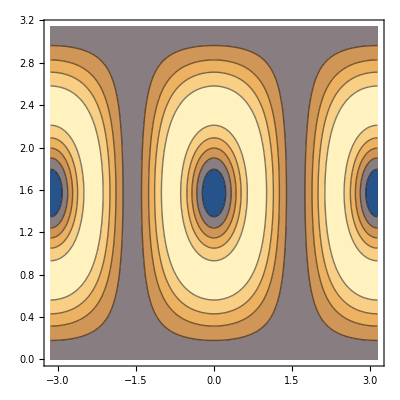

```mathematica
ContourPlot[mag/.{K22->0.02,K20->-0.1},{a,-Pi,Pi},{b,0,Pi}]
```

```mathematica
(*Finally, when is tau parallel to omega?*)
crossedTorque=Simplify[ExpToTrig[Norm[Cross[complextorque/.{ϕ->0,θ->Pi/2,r->1}, {Cos[a]Sin[b],Sin[a]Sin[b],Cos[b]}]]],Assumptions->{a>0,b>0,c>0}];
crossedTorque
cintcross = Integrate[crossedTorque^2, {c,0,2Pi}, Assumptions->{K22>0,K20<0}];
cintcross
```

3/2 √(4 Abs[Cos[a] (4 K22 Cos[2 a-c]-2 K22 Cos[2 a-b-c]+K20 Cos[b-c]-2 K22 Cos[b-c]-2 K22 Cos[2 a+b-c]-2 K20 Cos[c]-4 K22 Cos[c]+2 K20 Cos[2 a+c]+K20 Cos[2 a-b+c]+K20 Cos[b+c]-2 K22 Cos[b+c]+K20 Cos[2 a+b+c]) Sin[b]^2]^2+64 Abs[Cos[a] Sin[b] (Cos[c] Sin[a]+Cos[a] Cos[b] Sin[c]) (Cos[b] (K20+2 K22+4 K22 Cos[a] Cos[c])-4 K22 Sin[a] Sin[c])]^2+Abs[Sin[b] (4 Cos[a] Cos[b] Cos[c]-4 Sin[a] Sin[c]) (4 K22 Cos[a]^2 Cos[c]+2 K22 (-3+Cos[2 a]) Cos[c]-2 Cos[a] Cos[b] (K20-2 K22+4 K22 Sin[a] Sin[c]))]^2)

-9/4 (-96 π Cos[a]^2 Cos[b]^2 Im[K20]^2 Sin[b]^2+32 π Cos[a]^2 Cos[2 a] Cos[b]^2 Im[K20]^2 Sin[b]^2-16 π Cos[a]^2 Cos[2 a-2 b] Cos[b]^2 Im[K20]^2 Sin[b]^2-32 π Cos[a]^2 Cos[b]^2 Cos[2 b] Im[K20]^2 Sin[b]^2-16 π Cos[a]^2 Cos[b]^2 Cos[2 (a+b)] Im[K20]^2 Sin[b]^2-132 π Im[K22]^2 Sin[b]^2-240 π Cos[a]^2 Im[K22]^2 Sin[b]^2+92 π Cos[2 a] Im[K22]^2 Sin[b]^2+128 π Cos[a]^2 Cos[2 a] Im[K22]^2 Sin[b]^2-16 π Cos[2 a]^2 Im[K22]^2 Sin[b]^2-16 π Cos[a]^2 Cos[2 a]^2 Im[K22]^2 Sin[b]^2-12 π Cos[4 a] Im[K22]^2 Sin[b]^2+4 π Cos[2 a] Cos[4 a] Im[K22]^2 Sin[b]^2-46 π Cos[2 a-2 b] Im[K22]^2 Sin[b]^2-64 π Cos[a]^2 Cos[2 a-2 b] Im[K22]^2 Sin[b]^2+16 π Cos[2 a] Cos[2 a-2 b] Im[K22]^2 Sin[b]^2+16 π Cos[a]^2 Cos[2 a] Cos[2 a-2 b] Im[K22]^2 Sin[b]^2-2 π Cos[4 a] Cos[2 a-2 b] Im[K22]^2 Sin[b]^2-4 π Cos[2 a-2 b]^2 Im[K22]^2 Sin[b]^2-4 π Cos[a]^2 Cos[2 a-2 b]^2 Im[K22]^2 Sin[b]^2+6 π Cos[4 a-2 b] Im[K22]^2 Sin[b]^2-2 π Cos[2 a] Cos[4 a-2 b] Im[K22]^2 Sin[b]^2+π Cos[2 a-2 b] Cos[4 a-2 b] Im[K22]^2 Sin[b]^2-104 π Cos[2 b] Im[K22]^2 Sin[b]^2-224 π Cos[a]^2 Cos[2 b] Im[K22]^2 Sin[b]^2+36 π Cos[2 a] Cos[2 b] Im[K22]^2 Sin[b]^2+64 π Cos[a]^2 Cos[2 a] Cos[2 b] Im[K22]^2 Sin[b]^2-4 π Cos[4 a] Cos[2 b] Im[K22]^2 Sin[b]^2-18 π Cos[2 a-2 b] Cos[2 b] Im[K22]^2 Sin[b]^2-32 π Cos[a]^2 Cos[2 a-2 b] Cos[2 b] Im[K22]^2 Sin[b]^2+2 π Cos[4 a-2 b] Cos[2 b] Im[K22]^2 Sin[b]^2-20 π Cos[2 b]^2 Im[K22]^2 Sin[b]^2-48 π Cos[a]^2 Cos[2 b]^2 Im[K22]^2 Sin[b]^2-46 π Cos[2 (a+b)] Im[K22]^2 Sin[b]^2-64 π Cos[a]^2 Cos[2 (a+b)] Im[K22]^2 Sin[b]^2+16 π Cos[2 a] Cos[2 (a+b)] Im[K22]^2 Sin[b]^2+16 π Cos[a]^2 Cos[2 a] Cos[2 (a+b)] Im[K22]^2 Sin[b]^2-2 π Cos[4 a] Cos[2 (a+b)] Im[K22]^2 Sin[b]^2-8 π Cos[2 a-2 b] Cos[2 (a+b)] Im[K22]^2 Sin[b]^2-8 π Cos[a]^2 Cos[2 a-2 b] Cos[2 (a+b)] Im[K22]^2 Sin[b]^2+π Cos[4 a-2 b] Cos[2 (a+b)] Im[K22]^2 Sin[b]^2-18 π Cos[2 b] Cos[2 (a+b)] Im[K22]^2 Sin[b]^2-32 π Cos[a]^2 Cos[2 b] Cos[2 (a+b)] Im[K22]^2 Sin[b]^2-4 π Cos[2 (a+b)]^2 Im[K22]^2 Sin[b]^2-4 π Cos[a]^2 Cos[2 (a+b)]^2 Im[K22]^2 Sin[b]^2+6 π Cos[4 a+2 b] Im[K22]^2 Sin[b]^2-2 π Cos[2 a] Cos[4 a+2 b] Im[K22]^2 Sin[b]^2+π Cos[2 a-2 b] Cos[4 a+2 b] Im[K22]^2 Sin[b]^2+2 π Cos[2 b] Cos[4 a+2 b] Im[K22]^2 Sin[b]^2+π Cos[2 (a+b)] Cos[4 a+2 b] Im[K22]^2 Sin[b]^2-12 π Re[K20]^2 Sin[b]^2-24 π Cos[a]^2 Re[K20]^2 Sin[b]^2-8 π Cos[2 a] Re[K20]^2 Sin[b]^2+8 π Cos[a]^2 Cos[2 a] Re[K20]^2 Sin[b]^2+4 π Cos[2 a]^2 Re[K20]^2 Sin[b]^2-8 π Cos[2 a-2 b] Re[K20]^2 Sin[b]^2-4 π Cos[a]^2 Cos[2 a-2 b] Re[K20]^2 Sin[b]^2-π Cos[2 a-2 b]^2 Re[K20]^2 Sin[b]^2-16 π Cos[2 b] Re[K20]^2 Sin[b]^2-32 π Cos[a]^2 Cos[2 b] Re[K20]^2 Sin[b]^2+8 π Cos[a]^2 Cos[2 a] Cos[2 b] Re[K20]^2 Sin[b]^2-4 π Cos[2 a-2 b] Cos[2 b] Re[K20]^2 Sin[b]^2-4 π Cos[a]^2 Cos[2 a-2 b] Cos[2 b] Re[K20]^2 Sin[b]^2-4 π Cos[2 b]^2 Re[K20]^2 Sin[b]^2-8 π Cos[a]^2 Cos[2 b]^2 Re[K20]^2 Sin[b]^2-8 π Cos[2 (a+b)] Re[K20]^2 Sin[b]^2-4 π Cos[a]^2 Cos[2 (a+b)] Re[K20]^2 Sin[b]^2-2 π Cos[2 a-2 b] Cos[2 (a+b)] Re[K20]^2 Sin[b]^2-4 π Cos[2 b] Cos[2 (a+b)] Re[K20]^2 Sin[b]^2-4 π Cos[a]^2 Cos[2 b] Cos[2 (a+b)] Re[K20]^2 Sin[b]^2-π Cos[2 (a+b)]^2 Re[K20]^2 Sin[b]^2+48 π Re[K20] Re[K22] Sin[b]^2-96 π Cos[a]^2 Re[K20] Re[K22] Sin[b]^2+32 π Cos[2 a] Re[K20] Re[K22] Sin[b]^2+32 π Cos[a]^2 Cos[2 a] Re[K20] Re[K22] Sin[b]^2-16 π Cos[2 a]^2 Re[K20] Re[K22] Sin[b]^2+32 π Cos[2 a-2 b] Re[K20] Re[K22] Sin[b]^2-16 π Cos[a]^2 Cos[2 a-2 b] Re[K20] Re[K22] Sin[b]^2+4 π Cos[2 a-2 b]^2 Re[K20] Re[K22] Sin[b]^2+64 π Cos[2 b] Re[K20] Re[K22] Sin[b]^2-128 π Cos[a]^2 Cos[2 b] Re[K20] Re[K22] Sin[b]^2+32 π Cos[a]^2 Cos[2 a] Cos[2 b] Re[K20] Re[K22] Sin[b]^2+16 π Cos[2 a-2 b] Cos[2 b] Re[K20] Re[K22] Sin[b]^2-16 π Cos[a]^2 Cos[2 a-2 b] Cos[2 b] Re[K20] Re[K22] Sin[b]^2+16 π Cos[2 b]^2 Re[K20] Re[K22] Sin[b]^2-32 π Cos[a]^2 Cos[2 b]^2 Re[K20] Re[K22] Sin[b]^2+32 π Cos[2 (a+b)] Re[K20] Re[K22] Sin[b]^2-16 π Cos[a]^2 Cos[2 (a+b)] Re[K20] Re[K22] Sin[b]^2+8 π Cos[2 a-2 b] Cos[2 (a+b)] Re[K20] Re[K22] Sin[b]^2+16 π Cos[2 b] Cos[2 (a+b)] Re[K20] Re[K22] Sin[b]^2-16 π Cos[a]^2 Cos[2 b] Cos[2 (a+b)] Re[K20] Re[K22] Sin[b]^2+4 π Cos[2 (a+b)]^2 Re[K20] Re[K22] Sin[b]^2-132 π Re[K22]^2 Sin[b]^2-240 π Cos[a]^2 Re[K22]^2 Sin[b]^2+92 π Cos[2 a] Re[K22]^2 Sin[b]^2+128 π Cos[a]^2 Cos[2 a] Re[K22]^2 Sin[b]^2-16 π Cos[2 a]^2 Re[K22]^2 Sin[b]^2-16 π Cos[a]^2 Cos[2 a]^2 Re[K22]^2 Sin[b]^2-12 π Cos[4 a] Re[K22]^2 Sin[b]^2+4 π Cos[2 a] Cos[4 a] Re[K22]^2 Sin[b]^2-46 π Cos[2 a-2 b] Re[K22]^2 Sin[b]^2-64 π Cos[a]^2 Cos[2 a-2 b] Re[K22]^2 Sin[b]^2+16 π Cos[2 a] Cos[2 a-2 b] Re[K22]^2 Sin[b]^2+16 π Cos[a]^2 Cos[2 a] Cos[2 a-2 b] Re[K22]^2 Sin[b]^2-2 π Cos[4 a] Cos[2 a-2 b] Re[K22]^2 Sin[b]^2-4 π Cos[2 a-2 b]^2 Re[K22]^2 Sin[b]^2-4 π Cos[a]^2 Cos[2 a-2 b]^2 Re[K22]^2 Sin[b]^2+6 π Cos[4 a-2 b] Re[K22]^2 Sin[b]^2-2 π Cos[2 a] Cos[4 a-2 b] Re[K22]^2 Sin[b]^2+π Cos[2 a-2 b] Cos[4 a-2 b] Re[K22]^2 Sin[b]^2-104 π Cos[2 b] Re[K22]^2 Sin[b]^2-224 π Cos[a]^2 Cos[2 b] Re[K22]^2 Sin[b]^2+36 π Cos[2 a] Cos[2 b] Re[K22]^2 Sin[b]^2+64 π Cos[a]^2 Cos[2 a] Cos[2 b] Re[K22]^2 Sin[b]^2-4 π Cos[4 a] Cos[2 b] Re[K22]^2 Sin[b]^2-18 π Cos[2 a-2 b] Cos[2 b] Re[K22]^2 Sin[b]^2-32 π Cos[a]^2 Cos[2 a-2 b] Cos[2 b] Re[K22]^2 Sin[b]^2+2 π Cos[4 a-2 b] Cos[2 b] Re[K22]^2 Sin[b]^2-20 π Cos[2 b]^2 Re[K22]^2 Sin[b]^2-48 π Cos[a]^2 Cos[2 b]^2 Re[K22]^2 Sin[b]^2-46 π Cos[2 (a+b)] Re[K22]^2 Sin[b]^2-64 π Cos[a]^2 Cos[2 (a+b)] Re[K22]^2 Sin[b]^2+16 π Cos[2 a] Cos[2 (a+b)] Re[K22]^2 Sin[b]^2+16 π Cos[a]^2 Cos[2 a] Cos[2 (a+b)] Re[K22]^2 Sin[b]^2-2 π Cos[4 a] Cos[2 (a+b)] Re[K22]^2 Sin[b]^2-8 π Cos[2 a-2 b] Cos[2 (a+b)] Re[K22]^2 Sin[b]^2-8 π Cos[a]^2 Cos[2 a-2 b] Cos[2 (a+b)] Re[K22]^2 Sin[b]^2+π Cos[4 a-2 b] Cos[2 (a+b)] Re[K22]^2 Sin[b]^2-18 π Cos[2 b] Cos[2 (a+b)] Re[K22]^2 Sin[b]^2-32 π Cos[a]^2 Cos[2 b] Cos[2 (a+b)] Re[K22]^2 Sin[b]^2-4 π Cos[2 (a+b)]^2 Re[K22]^2 Sin[b]^2-4 π Cos[a]^2 Cos[2 (a+b)]^2 Re[K22]^2 Sin[b]^2+6 π Cos[4 a+2 b] Re[K22]^2 Sin[b]^2-2 π Cos[2 a] Cos[4 a+2 b] Re[K22]^2 Sin[b]^2+π Cos[2 a-2 b] Cos[4 a+2 b] Re[K22]^2 Sin[b]^2+2 π Cos[2 b] Cos[4 a+2 b] Re[K22]^2 Sin[b]^2+π Cos[2 (a+b)] Cos[4 a+2 b] Re[K22]^2 Sin[b]^2-48 K20 π Conjugate[K20] Cos[a]^2 Sin[b]^4-192 K22 π Conjugate[K22] Cos[a]^2 Sin[b]^4+16 K20 π Conjugate[K20] Cos[a]^2 Cos[2 a] Sin[b]^4+96 K22 π Conjugate[K20] Cos[a]^2 Cos[2 a] Sin[b]^4+96 K20 π Conjugate[K22] Cos[a]^2 Cos[2 a] Sin[b]^4+64 K22 π Conjugate[K22] Cos[a]^2 Cos[2 a] Sin[b]^4-32 K22 π Conjugate[K20] Cos[a]^2 Cos[2 a]^2 Sin[b]^4-32 K20 π Conjugate[K22] Cos[a]^2 Cos[2 a]^2 Sin[b]^4-32 K20 π Conjugate[K20] Cos[a]^4 Cos[2 b] Sin[b]^4-128 K22 π Conjugate[K22] Cos[a]^4 Cos[2 b] Sin[b]^4+64 K22 π Conjugate[K20] Cos[a]^4 Cos[2 a] Cos[2 b] Sin[b]^4+64 K20 π Conjugate[K22] Cos[a]^4 Cos[2 a] Cos[2 b] Sin[b]^4)

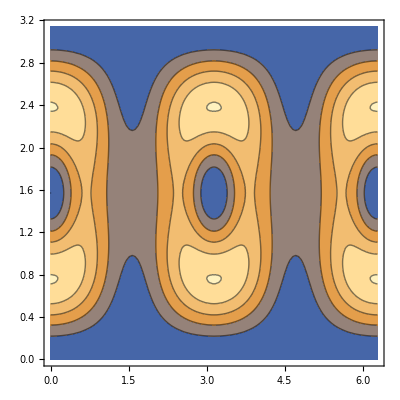

```mathematica
ContourPlot[cintcross/.{K22->0.02, K20->-0.1},{a,0,2Pi},{b,0,Pi}]
```

```mathematica
simptorque=Simplify[G m M/(2 RD^3) am^2  Sum[Sqrt[(2-mpp)!]Sqrt[(2+mpp)!]Conjugate[myWignerD[{2,0,mpp},a,b,c]]
({I,-1,0}(2-mpp+1)Klm[[mpp-1+4]]+{I,1,0}(2+mpp+1)Klm[[mpp+1+4]]+2{0,0,I}mpp Klm[[mpp+4]]),{mpp,-2,2}], Assumptions->{b>0, a>0, c>0}];
simptorque/(m am^2)
```

{-((0.+3.58379×10^13 ⅈ) ⅇ^(-ⅈ c) (-1.+1. ⅇ^(2 ⅈ c)) Sin[2 b])/RD^3,(2.5×10^-7 ⅇ^(-ⅈ c) (3.34487×10^20+3.34487×10^20 ⅇ^(2 ⅈ c)) Sin[2 b])/RD^3,((0.+4.77839×10^13 ⅈ) ⅇ^(-2 ⅈ c) (-1.+1. ⅇ^(4 ⅈ c)) Sin[b]^2)/RD^3}

```mathematica
Keq =Simplify[ Solve[Ixx==2/3 m am^2(k20-6kr22+1)&& Iyy==2/3 m am^2(k20+6kr22+1)&&Izz==2/3 m am^2(-2k20+1)&& Ixy==-2/3 m am^2(6 ki22)&& Ixz==2/3 m am^2(3kr21)&& Iyz==2/3 m am^2(3 ki21),{kr22, ki22, kr21, ki21,k20, am},Reals, Assumptions->{m>0, Ixx>0, Iyy>0,Izz>0,am>0}]][[1]]
```

{kr22→(-Ixx+Iyy)/(4 (Ixx+Iyy+Izz)),ki22→-Ixy/(2 (Ixx+Iyy+Izz)),kr21→Ixz/(Ixx+Iyy+Izz),ki21→Iyz/(Ixx+Iyy+Izz),k20→(Ixx+Iyy-2 Izz)/(2 (Ixx+Iyy+Izz)),am→(√((Ixx+Iyy+Izz)/m))/(√2)}

```mathematica
itorque=Simplify[simptorque/.Keq];
itorque//MatrixForm
```

(-(3 ⅇ^(-2 ⅈ c) G M (-2 ⅇ^(2 ⅈ c) Iyz+6 ⅇ^(2 ⅈ c) Iyz Cos[b]^2+(ⅈ (-1+ⅇ^(4 ⅈ c)) Ixz+(1+ⅇ^(4 ⅈ c)) Iyz) Sin[b]^2+ⅇ^(ⅈ c) ((1+ⅇ^(2 ⅈ c)) Ixy-ⅈ (-1+ⅇ^(2 ⅈ c)) (Iyy-Izz)) Sin[2 b]))/(4 RD^3)
(3 ⅇ^(-2 ⅈ c) G M (2 ⅇ^(2 ⅈ c) Ixz-6 ⅇ^(2 ⅈ c) Ixz Cos[b]^2+((1+ⅇ^(4 ⅈ c)) Ixz-ⅈ (-1+ⅇ^(4 ⅈ c)) Iyz) Sin[b]^2+ⅇ^(ⅈ c) (-((1+ⅇ^(2 ⅈ c)) Ixx)+ⅈ (-1+ⅇ^(2 ⅈ c)) Ixy+(1+ⅇ^(2 ⅈ c)) Izz) Sin[2 b]))/(4 RD^3)
-(3 ⅈ ⅇ^(-2 ⅈ c) G M ((-1+ⅇ^(4 ⅈ c)) Ixx-2 ⅈ Ixy-2 ⅈ ⅇ^(4 ⅈ c) Ixy+Iyy-ⅇ^(4 ⅈ c) Iyy+2 ⅇ^(ⅈ c) ((-1+ⅇ^(2 ⅈ c)) Ixz-ⅈ (1+ⅇ^(2 ⅈ c)) Iyz) Cot[b]) Sin[b]^2)/(4 RD^3))

```mathematica
Rz[a_]:={{Cos[a],-Sin[a],0},{Sin[a],Cos[a],0},{0,0,1}};
Ry[a_]:={{Cos[a],0,Sin[a]},{0,1,0},{-Sin[a],0,Cos[a]}};
R=Rz[-c].Ry[-b].Rz[-a];
Ig=Transpose[R].{{Ixx,Ixy,Ixz},{Ixy,Iyy,Iyz},{Ixz,Iyz,Izz}}.R;
firsttorque=(3 G M)/RD^3{-Ig[[3,2]],Ig[[3,1]],0}
```

{1/RD^3 3 G M (-((Cos[b] Cos[c] Sin[a]+Cos[a] Sin[c]) (Ixz Cos[b]-Ixx Cos[c] Sin[b]+Ixy Sin[b] Sin[c]))-(Cos[a] Cos[c]-Cos[b] Sin[a] Sin[c]) (Iyz Cos[b]-Ixy Cos[c] Sin[b]+Iyy Sin[b] Sin[c])-Sin[a] Sin[b] (Izz Cos[b]-Ixz Cos[c] Sin[b]+Iyz Sin[b] Sin[c])),1/RD^3 3 G M ((Cos[a] Cos[b] Cos[c]-Sin[a] Sin[c]) (Ixz Cos[b]-Ixx Cos[c] Sin[b]+Ixy Sin[b] Sin[c])+(-Cos[c] Sin[a]-Cos[a] Cos[b] Sin[c]) (Iyz Cos[b]-Ixy Cos[c] Sin[b]+Iyy Sin[b] Sin[c])+Cos[a] Sin[b] (Izz Cos[b]-Ixz Cos[c] Sin[b]+Iyz Sin[b] Sin[c])),0}

```mathematica
Simplify[((R).(firsttorque/.{Ixz->-Ixz, Ixy->-Ixy})-ComplexExpand[itorque])]
```

{0,0,0}

```mathematica
explicit={a->2,b->1,c->3,Ixx->0.4,Iyy->0.3,Izz->0.29,Ixy->0,Ixz->0,Iyz->0,RD->20,G->1,M->1};
R.firsttorque/.explicit
itorque/.explicit
```

{-2.406×10^-7,0.0000185666,-3.70963×10^-6}

{-2.406×10^-7+6.61744×10^-23 ⅈ,0.0000185666+0. ⅈ,-3.70963×10^-6-1.34946×10^-21 ⅈ}